```mathematica
(*Ising model*)
ns=10;nr=10*10;H=0;
sr:=2RandomReal[]-1;
xr:=RandomReal[];
Enflip[m_,n_]:=4(samp[[m-1,n]]samp[[m,n]]+samp[[m,n-1]]samp[[m,n]]+samp[[m+1,n]]samp[[m,n]]+samp[[m,n+1]]samp[[m,n]]+H samp[[m,n]]);M=500;

Table[m1tab=Table[samp=Table[If[xr<0.55,1,-1],{ns},{ns}];
Do[Do[If[Enflip[i,j]≤ 0,samp[[i,j]]=-samp[[i,j]],If[Exp[-Enflip[i,j]/T]>xr,samp[[i,j]]=-samp[[i,j]],samp[[i,j]]=samp[[i,j]]]],{i,2,ns-1},{j,2,ns-1}],{5}];Total[samp,2]/nr,{M}];{T,Mean[m1tab]//N},{T,{0.5,0.7,0.8,0.9,1,1.1,1.2,1.4,1.6,1.8,2,2.2,2.4,2.6,2.8,3,3.2,3.4}}]
```

{{0.5,0.24276},{0.7,0.30492},{0.8,0.32008},{0.9,0.28368},{1,0.24104},{1.1,0.2962},{1.2,0.27436},{1.4,0.25556},{1.6,0.24436},{1.8,0.24616},{2,0.21692},{2.2,0.22492},{2.4,0.23448},{2.6,0.24588},{2.8,0.24268},{3,0.22508},{3.2,0.18364},{3.4,0.21272}}

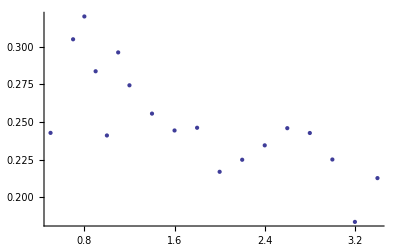

```mathematica
ListPlot[%,PlotRange->All]
```

```mathematica
(*10*10 Lattice, H=0, 75%  initial Magnt; T:0.1-> 4.7
5 round Thermalization, Average over 1000 samples per any round*)
n=10;H=0;
x:=RandomReal[];
flip1[u_,w_]:=2(samp[[u]][[w]]samp[[u-1]][[w]]+samp[[u]][[w]]samp[[u+1]][[w]]+samp[[u]][[w]]samp[[u]][[w-1]]+samp[[u]][[w]]samp[[u]][[w+1]]
+H samp[[u]][[w]]samp[[u]][[w]]);
r=Table[0,{u,1,12}];
l=Table[0,{u,1,12}];
t=Table[0,{w,1,10}];
b=Table[0,{w,1,10}];

M=1000;
Table[
M1tab=Table[
samp=Transpose[Append[Prepend[Transpose[Append[Prepend[Table[If[x<0.75,1,-1],{n},{n}],t],b]],l],r]];
Do[Do[If[flip1[u,w]≤0,samp[[u]][[w]]=-samp[[u]][[w]],If[Exp[-flip1[u,w]/T]>x,samp[[u]][[w]]=-samp[[u]][[w]],samp[[u]][[w]]=samp[[u]][[w]]]],{u,2,n},{w,2,n}],{5}];
Total[Total[samp]],{M}];{T,Mean[M1tab]/(n)^2//N},{T,{0.1,0.4,0.7,1,1.3,1.6,1.8,2,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,3,3.2,3.5,3.7,4,4.3,4.7}}]
```

```mathematica
{{0.1,0.89692},{0.4,0.88714},{0.7,0.88584},{1,0.87042},{1.3,0.85216},{1.6,0.77828},{1.8,0.71838},{2,0.62816},{2.1,0.59132},{2.2,0.53368},{2.3,0.47684},{2.4,0.41182},{2.5,0.37314},{2.6,0.34356},{2.7,0.30714},{2.8,0.27694},{3,0.22556},{3.2,0.19906},{3.5,0.17294},{3.7,0.16914},{4,0.15032},{4.3,0.14886},{4.7,0.13796}}
```

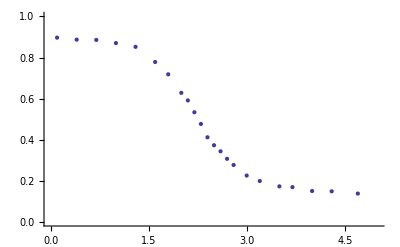

```mathematica
Show[ListPlot[%,PlotRange-> All],PlotRange-> {{0,5},{0,1}}]
```

```mathematica
(*30*30 Lattice, H=0, 85%  initial Magnt; T:0.1-> 4.7
5 round Thermalization, Average over 100 samples per any round*)
n=30;H=0;
x:=RandomReal[];
flip[u_,w_]:=2(samp[[u]][[w]]samp[[u-1]][[w]]+samp[[u]][[w]]samp[[u+1]][[w]]+samp[[u]][[w]]samp[[u]][[w-1]]+samp[[u]][[w]]samp[[u]][[w+1]]
+H samp[[u]][[w]]samp[[u]][[w]]);
r=Table[0,{u,1,32}];
l=Table[0,{u,1,32}];
t=Table[0,{w,1,30}];
b=Table[0,{w,1,30}];

M=100;
Table[
M1tab=Table[
samp=Transpose[Append[Prepend[Transpose[Append[Prepend[Table[If[x<0.85,1,-1],{n},{n}],t],b]],l],r]];
Do[Do[If[flip[u,w]≤0,samp[[u]][[w]]=-samp[[u]][[w]],If[Exp[-flip[u,w]/T]>x,samp[[u]][[w]]=-samp[[u]][[w]],samp[[u]][[w]]=samp[[u]][[w]]]],{u,2,n},{w,2,n}],{5}];
Total[Total[samp]],{M}];{T,Mean[M1tab]/(n)^2//N},{T,{0.1,0.4,0.7,1,1.3,1.6,1.8,2,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,3,3.2,3.5,3.7,4,4.3,4.7}}]
```

{{0.1,0.980244},{0.4,0.979711},{0.7,0.9792},{1,0.978689},{1.3,0.971089},{1.6,0.945244},{1.8,0.909222},{2,0.845333},{2.1,0.805578},{2.2,0.756022},{2.3,0.677711},{2.4,0.609089},{2.5,0.549},{2.6,0.450911},{2.7,0.370311},{2.8,0.294867},{3,0.215578},{3.2,0.128844},{3.5,0.0964889},{3.7,0.0809111},{4,0.0741778},{4.3,0.0713778},{4.7,0.0617333}}

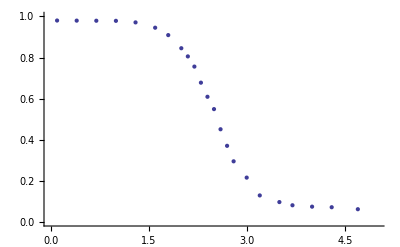

```mathematica
Show[ListPlot[%,PlotRange-> All],PlotRange->{{0,5},{0,1}}]
```

```mathematica
n=10;nr=2^n;H=0;T=0.05;
Print[" Exact Result Magnt.= ",n Sinh[H/T]/Sqrt[Sinh[H/T]^2+Exp[-4/T]]//N]
sr:=2(RandomInteger[]-1/2);
 Do[En1[n_]:=-Sum[s[i,j]s[i,j+1]+s[j+1,i]s[j,i],{i,n},{j,n-1}]-H Sum[s[i,j],{i,n},{j,n}];
Mag1[m_]:= Sum[s[i,j],{i,n},{j,n}];
M=40;
M1Ctab=Table[ensemble1=Table[sampi=Table[sr,{n}],{M}];
y=Total[Table[s[i_,j_]:=ensemble1[[u]][[n]];Exp[-En1[n]/T],{u,M}]];
M1=Total[Table[s[i_,j_]:=ensemble1[[u]][[n]];Exp[-En1[n]/T]Mag1[n]/y,{u,M}]//N
],{ 10}];
Print["          Crude MC Magnt.= ",Mean[M1Ctab]//N,"          ", Variance[M1Ctab//N]^0.5],{5}]
```

Exact Result Magnt.= 0.

Crude MC Magnt.= 1.5          11.3162

Crude MC Magnt.= -7.          12.7366

Crude MC Magnt.= -2.          22.5093

Crude MC Magnt.= 0.          12.693

Crude MC Magnt.= 5.5          17.8652

```mathematica
(*30*30 Lattice, H=0, 55%  initial Magnt; T=2
1 round Thermalization*)
```

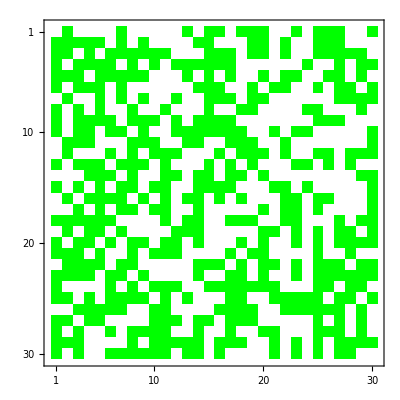

```mathematica
(*Magnt,before Thermlization*)
n=30;
xr:=RandomReal[];
samp=Table[If[x<0.55,1,-1],{n},{n}];
MatrixPlot[samp,ColorRules-> {1-> Green,-1-> White}]
```

```mathematica
(*Magnt;aftre Thermalization*)
```

```mathematica
T=2;H=0;
xr:=RandomReal[];
flip[u_,w_]:=2(samp[[u]][[w]]samp[[u-1]][[w]]+samp[[u]][[w]]samp[[u+1]][[w]]+samp[[u]][[w]]samp[[u]][[w-1]]+samp[[u]][[w]]samp[[u]][[w+1]]
+H samp[[u]][[w]]samp[[u]][[w]]);
```

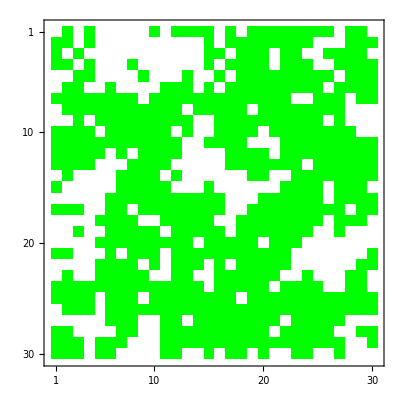

```mathematica
Do[If[flip[u,w]≤0,samp[[u]][[w]]=-samp[[u]][[w]],If[Exp[-flip1[u,w]/T]>xr,samp[[u]][[w]]=-samp[[u]][[w]],samp[[u]][[w]]=samp[[u]][[w]]]],{u,2,n-1},{w,2,n-1}]
MatrixPlot[samp,ColorRules->{1->Green,-1-> White}]
```

```mathematica
(*30*30 Lattice, H=0, 85%  initial Magnt; T=3
1 round Thermalization*)
```

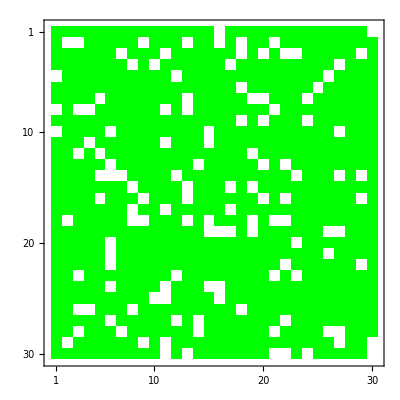

```mathematica
(*Magnt,before Thermlization*)
n=30;
xr:=RandomReal[];
samp=Table[If[x<0.85,1,-1],{n},{n}];
MatrixPlot[samp,ColorRules-> {1-> Green,-1-> White}]
```

```mathematica
(*Magnt;aftre Thermalization*)
```

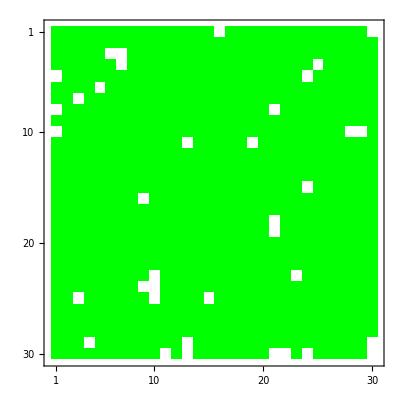

```mathematica
T=2;H=0;
xr:=RandomReal[];
flip[u_,w_]:=2(samp[[u]][[w]]samp[[u-1]][[w]]+samp[[u]][[w]]samp[[u+1]][[w]]+samp[[u]][[w]]samp[[u]][[w-1]]+samp[[u]][[w]]samp[[u]][[w+1]]
+H samp[[u]][[w]]samp[[u]][[w]]);Do[If[flip[u,w]≤0,samp[[u]][[w]]=-samp[[u]][[w]],If[Exp[-flip1[u,w]/T]>xr,samp[[u]][[w]]=-samp[[u]][[w]],samp[[u]][[w]]=samp[[u]][[w]]]],{u,2,n-1},{w,2,n-1}]
MatrixPlot[samp,ColorRules->{1->Green,-1-> White}]
```